Given u_2=((1+Max[(p_r(1+δ))/δ,c+p_r])/2-p_r-c)(1-Max[(p_r(1+δ))/δ,c+p_r])^++((c+p_r/δ)/2-c)(δ+1)/δ(p_r-δ c)^+,we have 

(1)If p_r<δ c,u_2=1/2 (-1+c+p_r)^2;
(2)If δ c<p_r<δ/(1+δ),u_2=(δ+c δ (-2+c+c δ)-2 δ p_r+(1+δ) p_r^2)/(2 δ);

```mathematica
(*Clean all exsiting variables*)
Clear["Global`*"]
```

```mathematica
(*Define u2: u2l for pr<δ c, u2g for δc<pr<δ/(1+δ)*)
u2l=1/2 (-1+c+Subscript[p, r])^2;
u2g=(δ+c δ (-2+c+c δ)-2 δ Subscript[p, r]+(1+δ) Subscript[p, r]^2)/(2 δ);
```

```mathematica
(*Define thresholds: ar,an,arn*)
ar[u2_]=(Subscript[p, r](1+δ)+δ u2)/(δ(1+u2));
an[u2_]=(c(1+δ)+ u2)/(1+u2);
arn[u2_]=(c+Subscript[p, r]+u2)/(1+u2);
```

```mathematica
(*Define expected matching probability when a∈[L,U]*)
q[a_,δ_]:=(1-a)/(1+δ);
Eqa[L_,U_]:=Integrate[q[a,δ] 1/(U-L),{a,L,U}]
```

```mathematica
(*Define revenue function: Rl for pr<δ c,Rg for δc<pr<δ/(1+δ)*)
Rl:= Simplify[Subscript[p, r](1-arn[u2l])+Subscript[p, r](1-arn[0])(1-(1-arn[u2l])(1+δ)Eqa[arn[u2l],1])]
Rg:= Simplify[Subscript[p, r](1-ar[u2g])+Subscript[p, r](1-ar[0])(1-(1-ar[u2g])(1+δ)Eqa[ar[u2g],1]-(ar[u2g]-an[u2g])Eqa[an[u2g],ar[u2g]])]
```

```mathematica
(*Define the second-order partial derivative of the revenue function with respect to pr*)
RevlDeri2:=D[Rl,{Subscript[p, r],2}]
RevgDeri2:=D[Rg,{Subscript[p, r],2}]
```

```mathematica
(*The second-order partial derivative of Rl is negative*)
{Reduce[RevlDeri2<0&&0<Subscript[p, r]<δ c&&δ>0&&c>0],Reduce[RevlDeri2>0&&0<Subscript[p, r]<δ c&&δ>0&&c>0]}
```

{p_r>0&&c>0&&δ>p_r/c,False}

```mathematica
(*The second-order partial derivative of Rg is negative*){Reduce[RevgDeri2<0&&δ c<Subscript[p, r]<=δ/(1+δ)&&0<=δ&&c>0,Subscript[p, r]],Reduce[RevgDeri2>0&&δ c<Subscript[p, r]<=δ/(1+δ)&&0<=δ&&c>0,Subscript[p, r]]}
```

{0<c<1&&0<δ<(1-c)/c&&c δ<p_r≤δ/(1+δ),False}

Thus, the revenue functions Rl and Rg are both concave;

```mathematica
(*Solve the interior point solution: Subscript[pr, l] for Rl*)
FullSimplify[Solve[D[Rl,Subscript[p, r]]==0&&0<Subscript[p, r]<=δ c&&0<=δ&&c>0,Subscript[p, r]]]
```

{{p_r→ConditionalExpression[Root[-39+101 c-129 c^2+111 c^3-65 c^4+27 c^5-7 c^6+c^7+(124-288 c+384 c^2-304 c^3+156 c^4-48 c^5+8 c^6) #1+(-159+435 c-522 c^2+354 c^3-135 c^4+27 c^5) #1^2+(162-392 c+396 c^2-200 c^3+50 c^4) #1^3+(-109+219 c-165 c^2+55 c^3) #1^4+(48-72 c+36 c^2) #1^5+(-13+13 c) #1^6+2 #1^7&,1], ]}}

```mathematica
(*Solve the interior point solution: Subscript[pr, g] for Rg*)
FullSimplify[Solve[D[Rg,Subscript[p, r]]==0&&δ c<Subscript[p, r]<=δ/(1+δ)&&0<=δ&&c>0,Subscript[p, r]]]
```

{{p_r→ConditionalExpression[Root[-39 δ^4+62 c δ^4-67 c^2 δ^4+44 c^3 δ^4-21 c^4 δ^4+6 c^5 δ^4-c^6 δ^4-31 c^2 δ^5+36 c^3 δ^5-30 c^4 δ^5+12 c^5 δ^5-3 c^6 δ^5-9 c^4 δ^6+6 c^5 δ^6-3 c^6 δ^6-c^6 δ^7+(78 δ^3-124 c δ^3+134 c^2 δ^3-88 c^3 δ^3+42 c^4 δ^3-12 c^5 δ^3+2 c^6 δ^3+124 δ^4-196 c δ^4+256 c^2 δ^4-184 c^3 δ^4+108 c^4 δ^4-36 c^5 δ^4+8 c^6 δ^4+98 c^2 δ^5-96 c^3 δ^5+90 c^4 δ^5-36 c^5 δ^5+12 c^6 δ^5+24 c^4 δ^6-12 c^5 δ^6+8 c^6 δ^6+2 c^6 δ^7) #1+(-123 δ^3+180 c δ^3-150 c^2 δ^3+60 c^3 δ^3-15 c^4 δ^3-159 δ^4+204 c δ^4-252 c^2 δ^4+120 c^3 δ^4-45 c^4 δ^4-102 c^2 δ^5+60 c^3 δ^5-45 c^4 δ^5-15 c^4 δ^6) #1^2+(46 δ^2-72 c δ^2+60 c^2 δ^2-24 c^3 δ^2+6 c^4 δ^2+200 δ^3-216 c δ^3+192 c^2 δ^3-72 c^3 δ^3+24 c^4 δ^3+162 δ^4-144 c δ^4+204 c^2 δ^4-72 c^3 δ^4+36 c^4 δ^4+72 c^2 δ^5-24 c^3 δ^5+24 c^4 δ^5+6 c^4 δ^6) #1^3+(-81 δ^2+54 c δ^2-27 c^2 δ^2-190 δ^3+108 c δ^3-81 c^2 δ^3-109 δ^4+54 c δ^4-81 c^2 δ^4-27 c^2 δ^5) #1^4+(18 δ-12 c δ+6 c^2 δ+84 δ^2-36 c δ^2+24 c^2 δ^2+114 δ^3-36 c δ^3+36 c^2 δ^3+48 δ^4-12 c δ^4+24 c^2 δ^4+6 c^2 δ^5) #1^5+(-13 δ-39 δ^2-39 δ^3-13 δ^4) #1^6+(2+8 δ+12 δ^2+8 δ^3+2 δ^4) #1^7&,1], ]}}

```mathematica
(*Define the interior point solution: Subscript[pr, l],Subscript[pr, g]*)Subscript[pr, l]=Root[-39+101 c-129 c^2+111 c^3-65 c^4+27 c^5-7 c^6+c^7+(124-288 c+384 c^2-304 c^3+156 c^4-48 c^5+8 c^6) #1+(-159+435 c-522 c^2+354 c^3-135 c^4+27 c^5) #1^2+(162-392 c+396 c^2-200 c^3+50 c^4) #1^3+(-109+219 c-165 c^2+55 c^3) #1^4+(48-72 c+36 c^2) #1^5+(-13+13 c) #1^6+2 #1^7&,1];Subscript[pr, g]=Root[-39 δ^4+62 c δ^4-67 c^2 δ^4+44 c^3 δ^4-21 c^4 δ^4+6 c^5 δ^4-c^6 δ^4-31 c^2 δ^5+36 c^3 δ^5-30 c^4 δ^5+12 c^5 δ^5-3 c^6 δ^5-9 c^4 δ^6+6 c^5 δ^6-3 c^6 δ^6-c^6 δ^7+(78 δ^3-124 c δ^3+134 c^2 δ^3-88 c^3 δ^3+42 c^4 δ^3-12 c^5 δ^3+2 c^6 δ^3+124 δ^4-196 c δ^4+256 c^2 δ^4-184 c^3 δ^4+108 c^4 δ^4-36 c^5 δ^4+8 c^6 δ^4+98 c^2 δ^5-96 c^3 δ^5+90 c^4 δ^5-36 c^5 δ^5+12 c^6 δ^5+24 c^4 δ^6-12 c^5 δ^6+8 c^6 δ^6+2 c^6 δ^7) #1+(-123 δ^3+180 c δ^3-150 c^2 δ^3+60 c^3 δ^3-15 c^4 δ^3-159 δ^4+204 c δ^4-252 c^2 δ^4+120 c^3 δ^4-45 c^4 δ^4-102 c^2 δ^5+60 c^3 δ^5-45 c^4 δ^5-15 c^4 δ^6) #1^2+(46 δ^2-72 c δ^2+60 c^2 δ^2-24 c^3 δ^2+6 c^4 δ^2+200 δ^3-216 c δ^3+192 c^2 δ^3-72 c^3 δ^3+24 c^4 δ^3+162 δ^4-144 c δ^4+204 c^2 δ^4-72 c^3 δ^4+36 c^4 δ^4+72 c^2 δ^5-24 c^3 δ^5+24 c^4 δ^5+6 c^4 δ^6) #1^3+(-81 δ^2+54 c δ^2-27 c^2 δ^2-190 δ^3+108 c δ^3-81 c^2 δ^3-109 δ^4+54 c δ^4-81 c^2 δ^4-27 c^2 δ^5) #1^4+(18 δ-12 c δ+6 c^2 δ+84 δ^2-36 c δ^2+24 c^2 δ^2+114 δ^3-36 c δ^3+36 c^2 δ^3+48 δ^4-12 c δ^4+24 c^2 δ^4+6 c^2 δ^5) #1^5+(-13 δ-39 δ^2-39 δ^3-13 δ^4) #1^6+(2+8 δ+12 δ^2+8 δ^3+2 δ^4) #1^7&,1];
```

```mathematica
(*Find the conditions for the optimal solution*)
{Reduce[0<Subscript[pr, l]<=δ c&&Subscript[pr, g]>δ c&&0<c&&δ>0],Reduce[0<Subscript[pr, l]<=δ c&&0<Subscript[pr, g]<=δ c&&0<c&&δ>0],Reduce[Subscript[pr, l]>δ c&&Subscript[pr, g]<=δ c&&0<c&&δ>0],Reduce[Subscript[pr, l]>δ c&&Subscript[pr, g]>=δ c&&0<c&&δ>0]}
```

{False,δ>0&&Root[-39+(101+124 δ) #1+(-129-288 δ-159 δ^2) #1^2+(111+384 δ+435 δ^2+162 δ^3) #1^3+(-65-304 δ-522 δ^2-392 δ^3-109 δ^4) #1^4+(27+156 δ+354 δ^2+396 δ^3+219 δ^4+48 δ^5) #1^5+(-7-48 δ-135 δ^2-200 δ^3-165 δ^4-72 δ^5-13 δ^6) #1^6+(1+8 δ+27 δ^2+50 δ^3+55 δ^4+36 δ^5+13 δ^6+2 δ^7) #1^7&,1]≤c<1,δ>0&&Root[-39+(140+124 δ) #1+(-191-350 δ-159 δ^2) #1^2+(178+518 δ+502 δ^2+162 δ^3) #1^3+(-109-436 δ-654 δ^2-436 δ^3-109 δ^4) #1^4+(48+240 δ+480 δ^2+480 δ^3+240 δ^4+48 δ^5) #1^5+(-13-78 δ-195 δ^2-260 δ^3-195 δ^4-78 δ^5-13 δ^6) #1^6+(2+14 δ+42 δ^2+70 δ^3+70 δ^4+42 δ^5+14 δ^6+2 δ^7) #1^7&,1]≤c<Root[-39+(101+124 δ) #1+(-129-288 δ-159 δ^2) #1^2+(111+384 δ+435 δ^2+162 δ^3) #1^3+(-65-304 δ-522 δ^2-392 δ^3-109 δ^4) #1^4+(27+156 δ+354 δ^2+396 δ^3+219 δ^4+48 δ^5) #1^5+(-7-48 δ-135 δ^2-200 δ^3-165 δ^4-72 δ^5-13 δ^6) #1^6+(1+8 δ+27 δ^2+50 δ^3+55 δ^4+36 δ^5+13 δ^6+2 δ^7) #1^7&,1],δ>0&&0<c≤Root[-39+(140+124 δ) #1+(-191-350 δ-159 δ^2) #1^2+(178+518 δ+502 δ^2+162 δ^3) #1^3+(-109-436 δ-654 δ^2-436 δ^3-109 δ^4) #1^4+(48+240 δ+480 δ^2+480 δ^3+240 δ^4+48 δ^5) #1^5+(-13-78 δ-195 δ^2-260 δ^3-195 δ^4-78 δ^5-13 δ^6) #1^6+(2+14 δ+42 δ^2+70 δ^3+70 δ^4+42 δ^5+14 δ^6+2 δ^7) #1^7&,1]}

Therefore, the optimal price pr^* will be 
(1) when c>c̄,pr*=pr_l;
(2)when c̲<c<c̄,pr*=δ c;
(3)when c<c̲,pr*=pr_g;

where c̄=Root[-39+(101+124 δ) #1+(-129-288 δ-159 δ^2) #1^2+(111+384 δ+435 δ^2+162 δ^3) #1^3+(-65-304 δ-522 δ^2-392 δ^3-109 δ^4) #1^4+(27+156 δ+354 δ^2+396 δ^3+219 δ^4+48 δ^5) #1^5+(-7-48 δ-135 δ^2-200 δ^3-165 δ^4-72 δ^5-13 δ^6) #1^6+(1+8 δ+27 δ^2+50 δ^3+55 δ^4+36 δ^5+13 δ^6+2 δ^7) #1^7&,1]

c̲=Root[-39+(140+124 δ) #1+(-191-350 δ-159 δ^2) #1^2+(178+518 δ+502 δ^2+162 δ^3) #1^3+(-109-436 δ-654 δ^2-436 δ^3-109 δ^4) #1^4+(48+240 δ+480 δ^2+480 δ^3+240 δ^4+48 δ^5) #1^5+(-13-78 δ-195 δ^2-260 δ^3-195 δ^4-78 δ^5-13 δ^6) #1^6+(2+14 δ+42 δ^2+70 δ^3+70 δ^4+42 δ^5+14 δ^6+2 δ^7) #1^7&,1]

#### Optimal pr

```mathematica
Clear["Global`*"]
Rl[pr_,c_]:=-((pr (-1+c+pr) (13+c^4+4 c^3 (-1+pr)-12 pr+10 pr^2-4 pr^3+pr^4+2 c^2 (5-6 pr+3 pr^2)+4 c (-3+5 pr-3 pr^2+pr^3)))/(3+c^2+2 c (-1+pr)-2 pr+pr^2)^2);
Rg[pr_,δ_,c_]:=-((pr (pr+(-1+pr) δ) (-4 pr^3 δ (1+δ)+pr^4 (1+δ)^2-4 pr δ^2 (3+c (-2+c+c δ))+2 pr^2 δ (3+5 δ+c (1+δ) (-2+c+c δ))+δ^2 (13+c (-2+c+c δ) (6+c (-2+c+c δ)))))/(δ (-2 pr δ+pr^2 (1+δ)+δ (3+c (-2+c+c δ)))^2));
prl[c_]:=Root[-39+101 c-129 c^2+111 c^3-65 c^4+27 c^5-7 c^6+c^7+(124-288 c+384 c^2-304 c^3+156 c^4-48 c^5+8 c^6) #1+(-159+435 c-522 c^2+354 c^3-135 c^4+27 c^5) #1^2+(162-392 c+396 c^2-200 c^3+50 c^4) #1^3+(-109+219 c-165 c^2+55 c^3) #1^4+(48-72 c+36 c^2) #1^5+(-13+13 c) #1^6+2 #1^7&,1];
prg[δ_,c_]:=Root[-39 δ^4+62 c δ^4-67 c^2 δ^4+44 c^3 δ^4-21 c^4 δ^4+6 c^5 δ^4-c^6 δ^4-31 c^2 δ^5+36 c^3 δ^5-30 c^4 δ^5+12 c^5 δ^5-3 c^6 δ^5-9 c^4 δ^6+6 c^5 δ^6-3 c^6 δ^6-c^6 δ^7+(78 δ^3-124 c δ^3+134 c^2 δ^3-88 c^3 δ^3+42 c^4 δ^3-12 c^5 δ^3+2 c^6 δ^3+124 δ^4-196 c δ^4+256 c^2 δ^4-184 c^3 δ^4+108 c^4 δ^4-36 c^5 δ^4+8 c^6 δ^4+98 c^2 δ^5-96 c^3 δ^5+90 c^4 δ^5-36 c^5 δ^5+12 c^6 δ^5+24 c^4 δ^6-12 c^5 δ^6+8 c^6 δ^6+2 c^6 δ^7) #1+(-123 δ^3+180 c δ^3-150 c^2 δ^3+60 c^3 δ^3-15 c^4 δ^3-159 δ^4+204 c δ^4-252 c^2 δ^4+120 c^3 δ^4-45 c^4 δ^4-102 c^2 δ^5+60 c^3 δ^5-45 c^4 δ^5-15 c^4 δ^6) #1^2+(46 δ^2-72 c δ^2+60 c^2 δ^2-24 c^3 δ^2+6 c^4 δ^2+200 δ^3-216 c δ^3+192 c^2 δ^3-72 c^3 δ^3+24 c^4 δ^3+162 δ^4-144 c δ^4+204 c^2 δ^4-72 c^3 δ^4+36 c^4 δ^4+72 c^2 δ^5-24 c^3 δ^5+24 c^4 δ^5+6 c^4 δ^6) #1^3+(-81 δ^2+54 c δ^2-27 c^2 δ^2-190 δ^3+108 c δ^3-81 c^2 δ^3-109 δ^4+54 c δ^4-81 c^2 δ^4-27 c^2 δ^5) #1^4+(18 δ-12 c δ+6 c^2 δ+84 δ^2-36 c δ^2+24 c^2 δ^2+114 δ^3-36 c δ^3+36 c^2 δ^3+48 δ^4-12 c δ^4+24 c^2 δ^4+6 c^2 δ^5) #1^5+(-13 δ-39 δ^2-39 δ^3-13 δ^4) #1^6+(2+8 δ+12 δ^2+8 δ^3+2 δ^4) #1^7&,1];
c1[δ_]:=Root[-39+(140+124 δ) #1+(-191-350 δ-159 δ^2) #1^2+(178+518 δ+502 δ^2+162 δ^3) #1^3+(-109-436 δ-654 δ^2-436 δ^3-109 δ^4) #1^4+(48+240 δ+480 δ^2+480 δ^3+240 δ^4+48 δ^5) #1^5+(-13-78 δ-195 δ^2-260 δ^3-195 δ^4-78 δ^5-13 δ^6) #1^6+(2+14 δ+42 δ^2+70 δ^3+70 δ^4+42 δ^5+14 δ^6+2 δ^7) #1^7&,1];
c2[δ_]:=Root[-39+(101+124 δ) #1+(-129-288 δ-159 δ^2) #1^2+(111+384 δ+435 δ^2+162 δ^3) #1^3+(-65-304 δ-522 δ^2-392 δ^3-109 δ^4) #1^4+(27+156 δ+354 δ^2+396 δ^3+219 δ^4+48 δ^5) #1^5+(-7-48 δ-135 δ^2-200 δ^3-165 δ^4-72 δ^5-13 δ^6) #1^6+(1+8 δ+27 δ^2+50 δ^3+55 δ^4+36 δ^5+13 δ^6+2 δ^7) #1^7&,1];
pr[c_,δ_]:=Piecewise[{{prl[c],c2[δ]<=c<1},{δ c,c1[δ]<c<c2[δ]},{prg[δ,c],0<c<=c1[δ]}}]
R[c_,δ_]:=Piecewise[{{Rl[prl[c],c],c2[δ]<=c<1},{Rg[δ c,δ,c],c1[δ]<c<c2[δ]},{Rg[prg[δ,c],δ,c],0<c<=c1[δ]}}]
```

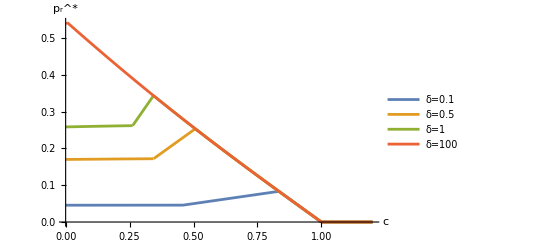

```mathematica
Plot[{pr[c,0.1],pr[c,0.5],pr[c,1],pr[c,100]},{c,0,1.2},PlotLegends->Placed[{"δ=0.1","δ=0.5","δ=1","δ=100"},{Scaled[{0.9,0.9}],{0.9,0.9}}],AxesLabel->{Style["c","Times",20],Style["p_r^*","Times",20]},LabelStyle->{FontSize->14,FontFamily->"Times"}]
```

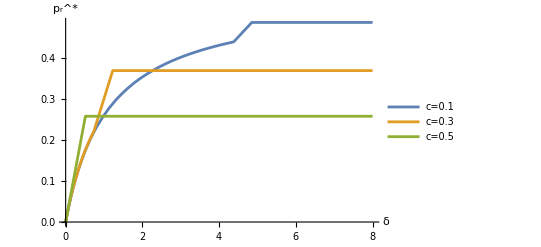

```mathematica
Plot[{pr[0.1,δ],pr[0.3,δ],pr[0.5,δ]},{δ,0,8},PlotLegends->Placed[{"c=0.1","c=0.3","c=0.5"},{Scaled[{0.9,0.2}],{0.9,0.2}}],AxesLabel->{Style["δ","Times",20],Style["p_r^*","Times",20]},LabelStyle->{FontSize->14,FontFamily->"Times"}]
```

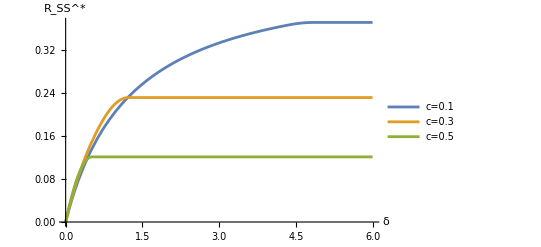

```mathematica
Plot[{R[0.1,δ],R[0.3,δ],R[0.5,δ]},{δ,0,6},PlotLegends->Placed[{"c=0.1","c=0.3","c=0.5"},{Scaled[{0.05,0.99}],{0.05,0.99}}],AxesLabel->{Style["δ","Times",20],Style["R_SS^*","Times",20]},LabelStyle->{FontSize->14,FontFamily->"Times"}]
```

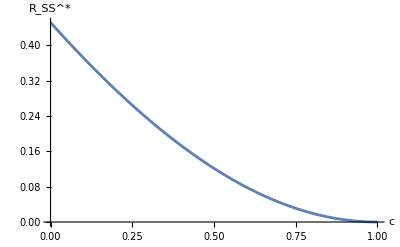

```mathematica
Plot[Rl[prl[c],c],{c,0,1},AxesLabel->{Style["c","Times",20],Style["R_SS^*","Times",20]},LabelStyle->{FontSize->14,FontFamily->"Times"}]
```

General::munfl: (2.04082×10^-7)^46 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.04082×10^-7)^47 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.04082×10^-7)^48 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

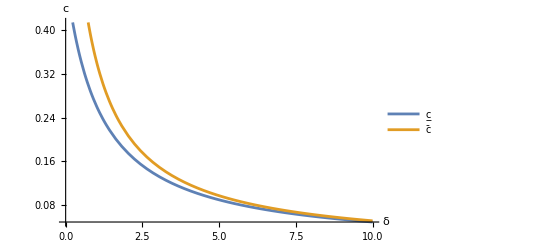

```mathematica
Plot[{c1[δ],c2[δ]},{δ,0,10},AxesLabel->{Style["δ","Times",20],Style["c","Times",20]},LabelStyle->{FontSize->14,FontFamily->"Times"},PlotLegends->Placed[{"c̲","c̄"},{Scaled[{0.9,0.9}],{0.9,0.9}}]]
```

```mathematica
OverBar[c]
```

c̄

```mathematica
UnderBar[c]
```

c̲